```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];
<<epi`;<<red`;
prF[expr_] := expr /. {
  (* Variables *)
  m0 -> Subscript[m, 0],
  m1 -> Subscript[m, 1],
  m2 -> Subscript[m, 2],
  mc -> Subscript[m, c],
  M1 -> Subscript[M, 1],
  M2 -> Subscript[M, 2],
  (* Parameters - Greek letters with subscripts *)
  Ph -> Φ,
  nu0 -> Subscript[ν, 0],
  nu1 -> Subscript[ν, 1],
  nu2 -> Subscript[ν, 2],
  nuc -> Subscript[ν, c],
  up1 -> Subscript[υ, 1],
  up2 -> Subscript[υ, 2],
  la1 -> Subscript[λ, 1],
  la2 -> Subscript[λ, 2],
  la1c -> Subscript[λ, "1,c"],
  la2c -> Subscript[λ, "2,c"],
  La1 -> Subscript[Λ, 1],
  La2 -> Subscript[Λ, 2],
al1 -> Subscript[α, 1],
  al2 -> Subscript[α, 2],
  be1 -> Subscript[β, 1],
  be2 -> Subscript[β, 2],
  ga1 -> Subscript[γ, 1],
  ga2 -> Subscript[γ, 2],
  be1c -> Subscript[β, 1c],
  be2c -> Subscript[β, 2c],ga1c -> Subscript[γ, 1c],
  ga2c -> Subscript[γ, 2c]
};


var={m0,m1,m2,mc,M1,M2};

(*Define lambda expressions for readability in RHS*)
cT={la1-> al1 m1+be1 mc+ ga1 M1,
la2-> al2 m2+ be2  mc+ ga2 M2,
la1c-> be1c  mc,
la2c-> be2c  mc,
La1-> ga1c  M1,
La2-> ga2c  M2};
(*Two-Strain Coinfection Model with Logistic Growth*)
RH={Ph-nu0*m0-m0*(la1+la2+la1c+la2c+La1+La2),-nu1*m1+m0*la1-m1*(la1+la2+la1c+la2c+La1+La2),-nu2*m2+m0*la2-m2*(la1+la2+la1c+la2c+La1+La2),-nuc*mc+m0*(la1c+la2c)+m1*(la2+la2c+La2)+m2*(la1+la1c+La1),-up1*M1+m0*La1+m1*(la1+la1c+La1),-up2*M2+m0*La2+m2*(la2+la2c+La2)};
RHS=RH/.cT;
{RN,rts,spe,alp,bet,gam,rnRed}=ODE2RN[RHS,var,prF];

RHS-gam.rts//FullSimplify  (*Should be {0,0,0,0}*)
mSi = minSiph[var, RN][[1]];
Print["minSiph=", mSi];
(* MAXIMAL ELIMINABLE SETS *)
{maxId, maxSets} = maxElim[RN, rts, var];
Print["reduced models are",maxSets];
IGMS[RN, mSi];
{RHS,var,par,cp,mSi,Jx,Jy,cDFE,E0,F,V,K,R0A,infVars}=bdAn[RN,rts,var];
F//MatrixForm
V//MatrixForm
```

28 reactions and rts=({}→{m_0} | Φ
{m_0}→^{m_1}{m_1} | m_0 m_1 α_1
{m_0}→^{M_1}{m_1} | m_0 M_1 γ_1
{m_0}→^{m_c}{m_1} | m_0 m_c β_1
{m_0}→^{m_2}{m_2} | m_0 m_2 α_2
{m_0}→^{M_2}{m_2} | m_0 M_2 γ_2
{m_0}→^{m_c}{m_2} | m_0 m_c β_2
{m_2}→^{m_1}{m_c} | m_1 m_2 α_1
{m_1}→^{m_2}{m_c} | m_1 m_2 α_2
{m_2}→^{M_1}{m_c} | m_2 M_1 (γ_1+γ_c)
{m_1}→^{M_2}{m_c} | m_1 M_2 (γ_2+γ_(2 c))
{m_0}→^{m_c}{m_c} | m_0 m_c (β_c+β_(2 c))
{m_1}→^{m_c}{m_c} | m_1 m_c (β_2+β_(2 c))
{m_2}→^{m_c}{m_c} | m_2 m_c (β_1+β_c)
{m_1}→^{m_1}{M_1} | m_1^2 α_1
{m_0}→^{M_1}{M_1} | m_0 M_1 γ_c
{m_1}→^{M_1}{M_1} | m_1 M_1 (γ_1+γ_c)
{m_1}→^{m_c}{M_1} | m_1 m_c (β_1+β_c)
{m_2}→^{m_2}{M_2} | m_2^2 α_2
{m_0}→^{M_2}{M_2} | m_0 M_2 γ_(2 c)
{m_2}→^{M_2}{M_2} | m_2 M_2 (γ_2+γ_(2 c))
{m_2}→^{m_c}{M_2} | m_2 m_c (β_2+β_(2 c))
{m_0}→{} | m_0 ν_0
{m_1}→{} | m_1 ν_1
{m_2}→{} | m_2 ν_2
{m_c}→{} | m_c ν_c
{M_1}→{} | M_1 υ_1
{M_2}→{} | M_2 υ_2)

{0,0,0,0,0,0}

minSiph={{m1,mc,M1},{m2,mc,M2}}

reduced models are{{mc,M1,M2},{m0}}

V ={{2 al1 m1-ga1 M1-ga1c M1+al2 m2+ga2 M2+ga2c M2+be2 mc+be2c mc+nu1,-ga1 m1-ga1c m1+up1,al2 m1,ga2 m1+ga2c m1,be2 m1+be2c m1},{2 al1 m1-ga1 M1-ga1c M1+al2 m2+ga2 M2+ga2c M2+be2 mc+be2c mc+nu1,-ga1 m1-ga1c m1+up1,al2 m1,ga2 m1+ga2c m1,be2 m1+be2c m1},{al1 m2,ga1 m2+ga1c m2,al1 m1+ga1 M1+ga1c M1+2 al2 m2-ga2 M2-ga2c M2+be1 mc+be1c mc+nu2,-ga2 m2-ga2c m2+up2,be1 m2+be1c m2},{al1 m2,ga1 m2+ga1c m2,al1 m1+ga1 M1+ga1c M1+2 al2 m2-ga2 M2-ga2c M2+be1 mc+be1c mc+nu2,-ga2 m2-ga2c m2+up2,be1 m2+be1c m2},{-al1 m2-al2 m2-ga2 M2-ga2c M2-be2 mc-be2c mc,-ga1 m2-ga1c m2,-al1 m1-al2 m1-ga1 M1-ga1c M1-be1 mc-be1c mc,-ga2 m1-ga2c m1,-be2 m1-be2c m1-be1 m2-be1c m2+nuc}} is singular

(al1 m0 | ga1c m0 | 0 | 0 | be1 m0
al1 m0 | ga1c m0 | 0 | 0 | be1 m0
0 | 0 | al2 m0 | ga2c m0 | be2 m0
0 | 0 | al2 m0 | ga2c m0 | be2 m0
0 | 0 | 0 | 0 | be1c m0+be2c m0)

(2 al1 m1-ga1 M1-ga1c M1+al2 m2+ga2 M2+ga2c M2+be2 mc+be2c mc+nu1 | -ga1 m1-ga1c m1+up1 | al2 m1 | ga2 m1+ga2c m1 | be2 m1+be2c m1
2 al1 m1-ga1 M1-ga1c M1+al2 m2+ga2 M2+ga2c M2+be2 mc+be2c mc+nu1 | -ga1 m1-ga1c m1+up1 | al2 m1 | ga2 m1+ga2c m1 | be2 m1+be2c m1
al1 m2 | ga1 m2+ga1c m2 | al1 m1+ga1 M1+ga1c M1+2 al2 m2-ga2 M2-ga2c M2+be1 mc+be1c mc+nu2 | -ga2 m2-ga2c m2+up2 | be1 m2+be1c m2
al1 m2 | ga1 m2+ga1c m2 | al1 m1+ga1 M1+ga1c M1+2 al2 m2-ga2 M2-ga2c M2+be1 mc+be1c mc+nu2 | -ga2 m2-ga2c m2+up2 | be1 m2+be1c m2
-al1 m2-al2 m2-ga2 M2-ga2c M2-be2 mc-be2c mc | -ga1 m2-ga1c m2 | -al1 m1-al2 m1-ga1 M1-ga1c M1-be1 mc-be1c mc | -ga2 m1-ga2c m1 | -be2 m1-be2c m1-be1 m2-be1c m2+nuc)

```mathematica
findCores[RN,3]
```

findCores[{0→m0,m0+m1→2 m1,m0+M1→m1+M1,m0+mc→m1+mc,m0+m2→2 m2,m0+M2→m2+M2,m0+mc→m2+mc,m1+m2→m1+mc,m1+m2→m2+mc,M1+m2→M1+mc,m1+M2→M2+mc,m0+mc→2 mc,m1+mc→2 mc,m2+mc→2 mc,2 m1→m1+M1,m0+M1→2 M1,m1+M1→2 M1,m1+mc→M1+mc,2 m2→m2+M2,m0+M2→2 M2,m2+M2→2 M2,m2+mc→M2+mc,m0→0,m1→0,m2→0,mc→0,M1→0,M2→0},3]

Inverse::sing: Matrix «1» is singular.

Inverse::sing: Matrix {{nu1,up1,0,0,0},{nu1,up1,0,0,0},{0,0,nu2,up2,0},{0,0,nu2,up2,0},{0,0,0,0,nuc}} is singular.

Inverse::sing: Matrix «1» is singular.

General::stop: Further output of Inverse::sing will be suppressed during this calculation.

28 reactions and rts=({}→{m_0} | Φ
{m_0}→^{m_1}{m_1} | m_0 m_1 α_1
{m_0}→^{M_1}{m_1} | m_0 M_1 γ_1
{m_0}→^{m_c}{m_1} | m_0 m_c β_1
{m_0}→^{m_2}{m_2} | m_0 m_2 α_2
{m_0}→^{M_2}{m_2} | m_0 M_2 γ_2
{m_0}→^{m_c}{m_2} | m_0 m_c β_2
{m_2}→^{m_1}{m_c} | m_1 m_2 α_1
{m_1}→^{m_2}{m_c} | m_1 m_2 α_2
{m_2}→^{M_1}{m_c} | m_2 M_1 (γ_1+γ_c)
{m_1}→^{M_2}{m_c} | m_1 M_2 (γ_2+γ_(2 c))
{m_0}→^{m_c}{m_c} | m_0 m_c (β_c+β_(2 c))
{m_1}→^{m_c}{m_c} | m_1 m_c (β_2+β_(2 c))
{m_2}→^{m_c}{m_c} | m_2 m_c (β_1+β_c)
{m_1}→^{m_1}{M_1} | m_1^2 α_1
{m_0}→^{M_1}{M_1} | m_0 M_1 γ_c
{m_1}→^{M_1}{M_1} | m_1 M_1 (γ_1+γ_c)
{m_1}→^{m_c}{M_1} | m_1 m_c (β_1+β_c)
{m_2}→^{m_2}{M_2} | m_2^2 α_2
{m_0}→^{M_2}{M_2} | m_0 M_2 γ_(2 c)
{m_2}→^{M_2}{M_2} | m_2 M_2 (γ_2+γ_(2 c))
{m_2}→^{m_c}{M_2} | m_2 m_c (β_2+β_(2 c))
{m_0}→{} | m_0 ν_0
{m_1}→{} | m_1 ν_1
{m_2}→{} | m_2 ν_2
{m_c}→{} | m_c ν_c
{M_1}→{} | M_1 υ_1
{M_2}→{} | M_2 υ_2)

{0,0,0,0,0,0}

minSiph={{m1,mc,M1},{m2,mc,M2}}

reduced models are{{mc,M1,M2},{m0}}

Minimal siphons: {T_1→{m1,mc,M1},T_2→{m2,mc,M2}}

IGMS edges: {1->2,2->1}

Cycles found: 1

Cycles: {{1->2,2->1}}

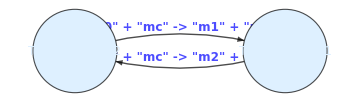

```mathematica
Print["RHS=",RHS//FullSimplify//MatrixForm, K//MatrixForm];
```

```mathematica
(*rnC[lhs_->rhs_]:=Module[{allVars,catTerms,catExpr,newL,newR},allVars=Union[Variables[lhs],Variables[rhs]];catTerms=Select[allVars,Coefficient[lhs,#]>0&&Coefficient[lhs,#]==Coefficient[rhs,#]&];If[catTerms==={},lhs->rhs,catExpr=Total[(Coefficient[lhs,#]#)&/@catTerms];newL=Expand[lhs-catExpr];newR=Expand[rhs-catExpr];Column[{Row[{"     ",catExpr}],If[newL===0,0,newL]->If[newR===0,0,newR]},Center]]];

rnS[RN_,alp_,bet_]:=Module[{catCoef,newAlp,newBet,result,coefToExpr},coefToExpr=Function[{coefs,vars},Module[{terms},terms=MapThread[If[#1>0,If[#1==1,#2,#1*#2],Nothing]&,{coefs,vars}];If[terms==={},{},terms]]];catCoef=MapThread[If[#1>0&&#2>0,Min[#1,#2],0]&,{alp,bet},2];newAlp=alp-catCoef;newBet=bet-catCoef;result=Table[Module[{catList,newL,newR,catExpr,lExpr,rExpr},catList=catCoef[[All,i]];newL=newAlp[[All,i]];newR=newBet[[All,i]];catExpr=coefToExpr[catList,var];lExpr=coefToExpr[newL,var];rExpr=coefToExpr[newR,var];If[catExpr==={},lExpr->rExpr,Row[{lExpr,Overscript[" → ",catExpr],rExpr}]]],{i,Length[RN]}];result];
Print["RN red=",Transpose[{rnS[RN,alp,bet],(Factor/@rts)}]//prF//MatrixForm];
*)
```